```mathematica
NS["MCsample_frequencies","C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
f0=Flatten@Import["stensola2_6mom_prior2_N1000.csv"];
```

```mathematica
Length@f0
```

1001

```mathematica
fs=Flatten@Import["stensola_activity_freqs_bins417641.csv"];
```

```mathematica
n=Length@fs-1;nn=Length@f0-1;
```

```mathematica
gm=Table[Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa],{a,0,n},{aa,0,nn}];
```

```mathematica
{(gm.f0-fs)/fs,fs}//T//MF;
```

```mathematica
fx=Table[Unique["xx"],nn+1];
```

```mathematica
fx[[;;5]]
```

{xx1012,xx1013,xx1014,xx1015,xx1016}

```mathematica
solf=Flatten@Solve[{gm.fx==0,Total[fx]==0},fx];
```

```mathematica
Save["solf",{solf,fx}];
```

```mathematica
<<"solf.m";
```

```mathematica
fxd=solf[[;;,1]]
```

{xx1947,xx1948,xx1949,xx1950,xx1951,xx1952,xx1953,xx1954,xx1955,xx1956,xx1957,xx1958,xx1959,xx1960,xx1961,xx1962,xx1963,xx1964,xx1965,xx1966,xx1967,xx1968,xx1969,xx1970,xx1971,xx1972,xx1973,xx1974,xx1975,xx1976,xx1977,xx1978,xx1979,xx1980,xx1981,xx1982,xx1983,xx1984,xx1985,xx1986,xx1987,xx1988,xx1989,xx1990,xx1991,xx1992,xx1993,xx1994,xx1995,xx1996,xx1997,xx1998,xx1999,xx2000,xx2001,xx2002,xx2003,xx2004,xx2005,xx2006,xx2007,xx2008,xx2009,xx2010,xx2011,xx2012}

```mathematica
fxtest=Array[a,7];solftest=Flatten@Solve[{RandomInteger[{-5,5},{3,7}].fxtest==0,Total[fxtest]==0},fxtest]
```

{a[4]→-(15 a[1])/7-(10 a[2])/7-(129 a[3])/14,a[5]→-2 a[1]-2 a[2]-(19 a[3])/2,a[6]→-a[1]/7-(10 a[2])/7-(17 a[3])/14,a[7]→(23 a[1])/7+(27 a[2])/7+(265 a[3])/14}

```mathematica
fxdtest=solftest[[;;,1]]
```

{a[4],a[5],a[6],a[7]}

```mathematica
fxitest=Complement[fxtest,fxdtest]
```

{a[1],a[2],a[3]}

```mathematica
test=(fxtest/.solftest)
```

{a[1],a[2],a[3],-(15 a[1])/7-(10 a[2])/7-(129 a[3])/14,-2 a[1]-2 a[2]-(19 a[3])/2,-a[1]/7-(10 a[2])/7-(17 a[3])/14,(23 a[1])/7+(27 a[2])/7+(265 a[3])/14}

```mathematica
Total[test]
```

0

```mathematica
testt=(test/.MapThread[Rule,{fxitest,Rationalize[RandomReal[{-0.000000000001,0.000000000001},Length@fxitest],0]}])
```

{35/104135097228978,65/165667101016921,112/135734765917105,-48539954522855859728668834412979/5463881641732499894021835419665719873574810,-10883732574708143827317396689141/1170831780371249977290393304214082830051745,-26398302168951163512318845302751/16391644925197499682065506258997159620724430,59784893439254663096507272675079/3278328985039499936413101251799431924144886}

```mathematica
Total@testt
```

0

```mathematica
Length@fxd
```

66

```mathematica
fxi=Complement[fx,fxd];ni=Length@fxi
```

935

```mathematica
argument=(fx/.solf);
```

```mathematica
testt=(test/.MapThread[Rule,{fxi,Rationalize[RandomReal[{-0.000000001,0.000000001},ni],0]}]);
```

```mathematica
Total@testt
```

0

```mathematica
ord=Ordering[Flatten@{fxd,fxi}];
```

```mathematica
ClearAll[repl];
repl=Function[Evaluate[fxi],Evaluate[argument]];
```

```mathematica
Length[repl@@(RandomReal[{-0.5,0.5},ni])]
```

1001

```mathematica
(repl@@(RandomReal[{-0.1,0.1},ni]))[[1000]]
```

-1.7247×10^104

```mathematica
Total[repl@@(RandomReal[{-0.1,0.1},ni])]
```

-3.88349×10^105

```mathematica
fr=2*Table[(1-aa+nn)/((nn+1)*(nn+2)),{aa,0,nn}];
Length@fr
```

1001

```mathematica
xlny[x_,y_]:=If[x>0,x*Log[x/y],0];
SetAttributes[xlny,Listable];
```

```mathematica
h[x_,y_]:=Total[xlny[x,y]]
```

```mathematica
<<"mcmc.m";
```

```mathematica
logpr=100*h[(#/Total@#)&@(f0+Rationalize[argument,0]),fr];
```

```mathematica
vars=T[{fxi,Table[-10^-4,ni],Table[10^-4,ni],Table[Reals,ni]}];
```

```mathematica
nsamples=1000;mcmc=MCMC[logpr,vars,nsamples(*,"ProgressMonitor"->None*)];
```

```mathematica
valuese=mcmc["ParameterRun"];
```

```mathematica
Dimensions[valuese]
```

{1000,935}

```mathematica
dfreqs=Table[repl@@(valuese[[i]]),{i,2,nsamples}];
```

```mathematica
freqs=Prepend[(f0+#)&/@dfreqs,f0];
```

```mathematica
Save["sampledfreqs1000e-4.m",freqs];
```

```mathematica
<<"sampledfreqs1000e-3.m";nsamples=1000;
```

```mathematica
nn=1000;rg=0.15;plot=ListPlot[Append[freqs,f0][[;;;;Round[nsamples/100],;;Round[rg*nn+1]]]*nn,Joined->True, PlotRange->All,DataRange->{0,rg*100},PlotMarkers->●,PlotStyle->Append[Table[{solid,Black,Opacity[0.05]},100],{solid,blue,Opacity[0.75]}],Epilog->Text["N = 1000, 100 samples",Scaled[{0.9,0.9}]],FrameLabel->{"total normalized activity/%","frequency density"},ImageSize->a4shortside];
expdf["stensola_N1000_MCsamples_blue_r015",plot];
```

```mathematica
expdf["stensola_N1000_MCsamples_blue",plot];
```

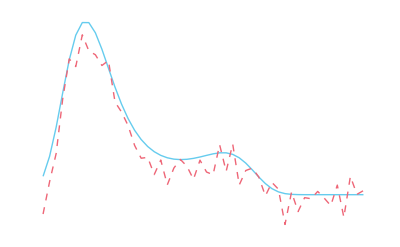

```mathematica
ListPlot[{f0,(Mean@freqs)}[[;;,;;50]],Joined->True,PlotRange->All]
```